-(-1)^(3/4) ⅇ^(-1/2 ⅈ n π+ⅈ Y) √(2/π) √(1/Y)

Cos[(n π)/2+Y Sin[θin]]

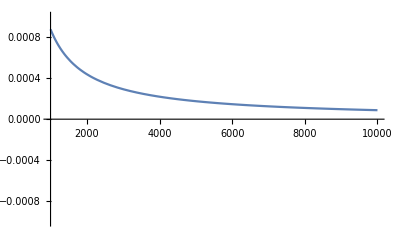

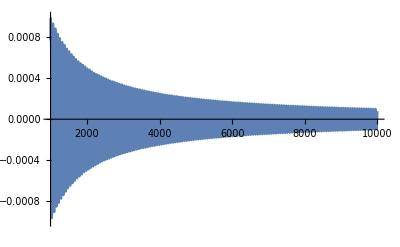

```mathematica
ClearAll[hankeln]

$Assumptions={X>0,Y>0,n∈Integers,θin∈Reals,Y0>0};
hankeln[Y_] = Normal@Series[
HankelH1[n,R]/.R->Normal@Series[√(X^2+Y^2),{Y,∞,0}]
,{Y,∞,1}]
angular[Y_] =Normal@Series[
Cos[Y Sin[θin]+n arc]/.arc->Normal@Series[ ArcTan[X,Y],{Y,∞,1}]
,{X,0,0}]


Plot[
Abs[HankelH1[n,Sqrt[X^2+Y^2]]- hankeln[Y]]/(Abs@HankelH1[n,Sqrt[X^2+Y^2]])/.{n->1,X->1,θin-> 0.1}
,{Y,1000.,10000.1},PlotRange-> 0.001]
Plot[
Cos[Y Sin[θin]+n ArcTan[X,Y]]-angular[Y]/.{n->1,X->1,θin-> 0.1}
,{Y,1000.,10000.1},PlotRange-> 0.001]
(*Plot[Cos[Y Sin[θin]+n ArcTan[X,Y]]-(Cos[Y Sin[θin]+n π/2]+n X/Y Sin[Y Sin[θin]+n π/2]) /.{n->1,X->1,θin-> 0.1},{Y,10.,1000.1}];*)
```

```mathematica
(*Integrate[hankeln[Y]Cos[Y Sin[θin]+n π/2]+n X/Y Sin[Y Sin[θin]+n π/2],{Y,Y0,∞}]
 Series[%,{Y0,∞,1}]//Normal//FullSimplify
*)
(*int=Integrate[hankeln[Y]Cos[Y Sin[θin]+n π/2] ,{Y,Y0,∞}]
Bapp =  Series[%,{Y0,∞,1}]//Normal//FullSimplify;*)
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in Y near {Y} = {-4.81043×10^7}. NIntegrate obtained 0.0727108+0.0632853 ⅈ and 0.00033513 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in Y near {Y} = {-4.81048×10^7}. NIntegrate obtained -0.0694922-0.0394853 ⅈ and 0.000335105 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in Y near {Y} = {-4.81053×10^7}. NIntegrate obtained 0.0682883+0.0374968 ⅈ and 0.00118345 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

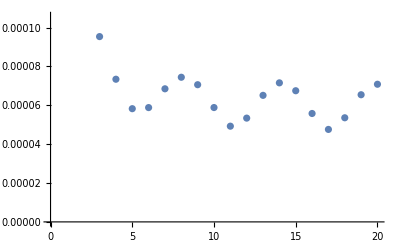

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in Y near {Y} = {4.81053×10^7}. NIntegrate obtained -0.00698507+0.0349538 ⅈ and 0.000295828 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in Y near {Y} = {4.81058×10^7}. NIntegrate obtained 0.0160175-0.0174899 ⅈ and 0.000266902 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in Y near {Y} = {4.81063×10^7}. NIntegrate obtained -0.0119804+0.00256781 ⅈ and 0.000246659 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

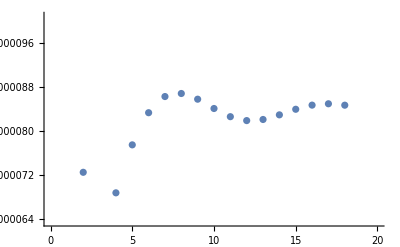

```mathematica
ClearAll[F,Bapp,B,Bend,error1,error2]

k=1.0;
a12 = 1.0;
(*Bapp[n_,X_,Y0_,θin_:0.0]=2.0(-1.0)^n 1/(√π √Y0)(1/2+ⅈ/2) (-1)^n ⅇ^(-ⅈ Y0 (-1+Sin[θin])) Sec[θin] (Sec[θin]+(-1)^n ⅇ^(2 ⅈ Y0 Sin[θin]) (Sec[θin]-Tan[θin])+Tan[θin]);*)

Bapp[n_,X_,Y0_,θin_:0.0]=(1+ⅈ)/(√(π Y0) Cos[θin]^2)  ⅇ^(ⅈ  Y0 (1-Sin[θin])) (1+(-1)^n ⅇ^(2 ⅈ Y0 Sin[θin]) (1-Sin[θin])+Sin[θin]);
F[n_,X_,Y_]:= (-1)^n Exp[ⅈ n ArcTan[X,Y] ]HankelH1[n,Sqrt[X^2+Y^2]]

B[n_,X_,θin_:0.0]:=NIntegrate[Boole[Y^2>k^2a12^2 - X^2 ] ⅇ^(ⅈ Y Sin[θin])F[n,X,Y],{Y,-∞,∞}]
Bend[n_,X_,Y0_,θin_:0.0]:=NIntegrate[Boole[Y^2>Y0^2 ] ⅇ^(ⅈ Y Sin[θin])F[n,X,Y],{Y,-∞,∞}]

error0[Y0_]:=(
args = {1,0.0,Y0,0.8};
B0=Abs@B[args[[1]],args[[2]],args[[4]]];
Abs[Bend@@args - Bapp@@args]/B0
)
error1[Y0_]:=(
args = {0,1.0,Y0,0.1};
B0=Abs@B[args[[1]],args[[2]],args[[4]]];
Abs[Bend@@args - Bapp@@args]/B0
)

ListPlot[error0/@Range[100.,10000.,500.]]
ListPlot[error1/@Range[100.,10000.,500.]]
```

```mathematica
ClearAll[F,S,S2]
F[n_,X_,Y_]:= (-1)^n Exp[ⅈ n ArcTan[X,Y] ]HankelH1[n,Sqrt[X^2+Y^2]]

S[n_,X_,θin_:0.0]:=NIntegrate[ⅇ^(ⅈ Y Sin[θin])F[n,X,Y],{Y,-∞,∞}]
S2[n_,X_,θin_:0.0] := 2 ⅈ^n ⅇ^(-ⅈ n θin)/Cos[θin] ⅇ^(ⅈ X Cos[θin])
S2[#,0.2]-S[#,0.2]&/@Range[0,3] 

S2[#,20.,0.3]-S[#,20.,0.3]&/@Range[0,3]
```

{-1.57274×10^-11+6.18905×10^-12 ⅈ,1.19282×10^-10-5.23253×10^-11 ⅈ,-1.48841×10^-11+9.94538×10^-13 ⅈ,-7.5534×10^-13+1.85718×10^-12 ⅈ}

{2.02895×10^-11-9.13269×10^-13 ⅈ,-6.54682×10^-12-8.36131×10^-12 ⅈ,9.91429×10^-13+2.12161×10^-11 ⅈ,-7.61324×10^-12-1.59754×10^-11 ⅈ}

```mathematica
n=0;X=2.4; θin=0.2;
B[n,X,θin]
S2[n,X,θin]
```

-1.43714+1.44879 ⅈ

-1.43714+1.44879 ⅈ

```mathematica
2 ⅈ^n ⅇ^(-ⅈ n θin)/Cos[θin] ⅇ^(ⅈ X Cos[θin])
```

1.88587+0.779666 ⅈ

```mathematica
ClearAll[n,x,integrateA,X,Y]
k= 1; a=1;
keff = 1+1ⅈ;
A[n_,x_] = ⅈ^n ⅇ^(-ⅈ n 0.1)ⅇ^(ⅈ x keff);
F[n_,X_,Y_]= (-1)^n Exp[ⅈ n ArcTan[X,Y] ]HankelH1[n,Sqrt[X^2+Y^2]];

integrateA[m_,x_,θin_:0, M_:0]:=Sum[
 NIntegrate[
Boole[(x2- x)^2+ y2^2>Abs[k]^2a^2 ]A[n,x2]F[n-m, x2- x, y2]
,{y2,-∞,∞},{x2,0,∞}]
,{n,-M,M}]
```

```mathematica
xs = Range[0.0,2.0,0.1]
result = integrateA[0,#]&/@xs
```

{0.,0.1,0.2,0.3,0.4,0.5,0.6,0.7,0.8,0.9,1.,1.1,1.2,1.3,1.4,1.5,1.6,1.7,1.8,1.9,2.}

{-0.538639+0.835824 ⅈ,-0.551074+0.825731 ⅈ,-0.560899+0.81599 ⅈ,-0.567923+0.807288 ⅈ,-0.571963+0.800298 ⅈ,-0.572795+0.795707 ⅈ,-0.570064+0.794256 ⅈ,-0.563148+0.796809 ⅈ,-0.550835+0.804481 ⅈ,-0.530408+0.818955 ⅈ,-0.4917+0.843859 ⅈ,-0.432583+0.884943 ⅈ,-0.400436+0.935043 ⅈ,-0.394073+0.989052 ⅈ,-0.411785+1.04242 ⅈ,-0.451439+1.09116 ⅈ,-0.510563+1.13185 ⅈ,-0.586435+1.16164 ⅈ,-0.676154+1.17822 ⅈ,-0.776716+1.1798 ⅈ,-0.885068+1.16509 ⅈ}

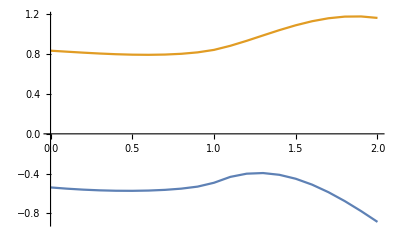

```mathematica
ListPlot[ {{xs,Re[result]}ᵀ,{xs,Im[result]}ᵀ},Joined->True]
```

{-0.538639+0.835824 ⅈ,-0.551074+0.825731 ⅈ,-0.560899+0.81599 ⅈ,-0.567923+0.807288 ⅈ,-0.571963+0.800298 ⅈ,-0.572795+0.795707 ⅈ,-0.570064+0.794256 ⅈ,-0.563148+0.796809 ⅈ,-0.550835+0.804481 ⅈ,-0.530408+0.818955 ⅈ,-0.4917+0.843859 ⅈ,-0.432583+0.884943 ⅈ,-0.400436+0.935043 ⅈ,-0.394073+0.989052 ⅈ,-0.411785+1.04242 ⅈ,-0.451439+1.09116 ⅈ,-0.510563+1.13185 ⅈ,-0.586435+1.16164 ⅈ,-0.676154+1.17822 ⅈ,-0.776716+1.1798 ⅈ,-0.885068+1.16509 ⅈ,-0.998173+1.13329 ⅈ,-1.11305+1.08403 ⅈ,-1.22683+1.01735 ⅈ,-1.33678+0.933674 ⅈ,-1.44035+0.833751 ⅈ,-1.53517+0.718642 ⅈ,-1.61913+0.58967 ⅈ,-1.69032+0.448386 ⅈ,-1.74713+0.296533 ⅈ,-1.78818+0.136009 ⅈ,-1.81237-0.0311665 ⅈ,-1.81889-0.202887 ⅈ,-1.8072-0.376992 ⅈ,-1.777-0.551297 ⅈ,-1.7283-0.723627 ⅈ,-1.66132-0.891839 ⅈ,-1.57657-1.05385 ⅈ,-1.47476-1.20767 ⅈ,-1.35682-1.3514 ⅈ,-1.22389-1.48329 ⅈ,-1.07731-1.60173 ⅈ,-0.918537-1.70527 ⅈ,-0.749215-1.79262 ⅈ,-0.571091-1.86272 ⅈ,-0.386017-1.91468 ⅈ,-0.195925-1.94781 ⅈ,-0.00280071-1.96166 ⅈ,0.191334-1.95596 ⅈ,0.384447-1.93069 ⅈ,0.574517-1.88601 ⅈ,0.759555-1.82231 ⅈ,0.937626-1.74019 ⅈ,1.10687-1.64043 ⅈ,1.26552-1.52399 ⅈ,1.41191-1.39204 ⅈ,1.54452-1.24588 ⅈ,1.66197-1.08698 ⅈ,1.76303-0.916919 ⅈ,1.84663-0.737416 ⅈ,1.91191-0.550276 ⅈ,1.95818-0.357384 ⅈ,1.98493-0.160685 ⅈ,1.99188+0.0378378 ⅈ,1.97893+0.236181 ⅈ,1.9462+0.432343 ⅈ,1.894+0.624347 ⅈ,1.82283+0.810253 ⅈ,1.7334+0.988189 ⅈ,1.6266+1.15636 ⅈ,1.50348+1.31307 ⅈ,1.36528+1.45673 ⅈ,1.21338+1.5859 ⅈ,1.04929+1.69928 ⅈ,0.874662+1.79573 ⅈ,0.691233+1.87426 ⅈ,0.500843+1.93409 ⅈ,0.305396+1.97461 ⅈ,0.10685+1.99541 ⅈ,-0.0928077+1.99628 ⅈ,-0.291578+1.9772 ⅈ,-0.487472+1.93836 ⅈ,-0.678527+1.88015 ⅈ,-0.86283+1.80314 ⅈ,-1.03854+1.70811 ⅈ,-1.20389+1.596 ⅈ,-1.35723+1.46793 ⅈ,-1.49703+1.32518 ⅈ,-1.62188+1.16917 ⅈ,-1.73053+1.00147 ⅈ,-1.82191+0.823756 ⅈ,-1.89508+0.637796 ⅈ,-1.94932+0.445452 ⅈ,-1.98409+0.248646 ⅈ,-1.99904+0.0493467 ⅈ,-1.99402-0.150455 ⅈ,-1.96907-0.348761 ⅈ,-1.92444-0.54359 ⅈ,-1.86059-0.732994 ⅈ,-1.77814-0.91508 ⅈ,-1.67792-1.08803 ⅈ,-1.56094-1.25011 ⅈ,-1.42836-1.3997 ⅈ,-1.2815-1.53531 ⅈ,-1.12184-1.65559 ⅈ,-0.950961-1.75932 ⅈ,-0.770581-1.84548 ⅈ,-0.5825-1.91319 ⅈ,-0.388596-1.9618 ⅈ,-0.190807-1.9908 ⅈ,0.00889057-1.99991 ⅈ,0.208501-1.98904 ⅈ,0.40603-1.95829 ⅈ,0.599503-1.90798 ⅈ,0.786987-1.8386 ⅈ,0.96661-1.75086 ⅈ,1.13658-1.64561 ⅈ,1.29518-1.52393 ⅈ,1.44085-1.38702 ⅈ,1.57213-1.23624 ⅈ,1.68769-1.07312 ⅈ,1.7864-0.899273 ⅈ,1.86725-0.71644 ⅈ,1.92945-0.526448 ⅈ,1.97237-0.331196 ⅈ,1.99558-0.132634 ⅈ,1.99885+0.0672536 ⅈ,1.98216+0.26647 ⅈ,1.94565+0.463023 ⅈ,1.88971+0.654951 ⅈ,1.81488+0.840335 ⅈ,1.72192+1.01732 ⅈ,1.61176+1.18415 ⅈ,1.48549+1.33914 ⅈ,1.34438+1.48075 ⅈ,1.18984+1.60757 ⅈ,1.0234+1.71832 ⅈ,0.846745+1.81191 ⅈ,0.661626+1.88739 ⅈ,0.469897+1.94401 ⅈ,0.273472+1.98121 ⅈ,0.0743149+1.99862 ⅈ,-0.125585+1.99605 ⅈ,-0.32423+1.97354 ⅈ,-0.519635+1.93131 ⅈ,-0.709849+1.86979 ⅈ,-0.89297+1.78958 ⅈ,-1.06717+1.69149 ⅈ,-1.2307+1.5765 ⅈ,-1.38194+1.44576 ⅈ,-1.51938+1.30057 ⅈ,-1.64163+1.14239 ⅈ,-1.74747+0.972796 ⅈ,-1.83586+0.79348 ⅈ,-1.90591+0.606236 ⅈ,-1.95691+0.412934 ⅈ,-1.98835+0.215507 ⅈ,-1.99994+0.015926 ⅈ,-1.99153-0.183814 ⅈ,-1.96323-0.381717 ⅈ,-1.91532-0.575807 ⅈ,-1.84827-0.764143 ⅈ,-1.76274-0.944844 ⅈ,-1.65961-1.1161 ⅈ,-1.5399-1.27621 ⅈ,-1.40479-1.42357 ⅈ,-1.25566-1.5567 ⅈ,-1.09397-1.67428 ⅈ,-0.921357-1.77513 ⅈ,-0.739536-1.85825 ⅈ,-0.550327-1.92279 ⅈ,-0.355618-1.96813 ⅈ,-0.157356-1.9938 ⅈ,0.0424777-1.99955 ⅈ,0.241887-1.98532 ⅈ,0.43888-1.95125 ⅈ,0.631488-1.89769 ⅈ,0.817785-1.82516 ⅈ,0.995912-1.7344 ⅈ,1.16409-1.62631 ⅈ,1.32063-1.50197 ⅈ,1.46398-1.36263 ⅈ,1.5927-1.20967 ⅈ,1.70551-1.04462 ⅈ,1.80128-0.869131 ⅈ,1.87905-0.684961 ⅈ,1.93804-0.493947 ⅈ,1.97767-0.297998 ⅈ,1.99754-0.0990713 ⅈ,1.99746+0.100845 ⅈ,1.97741+0.299754 ⅈ,1.9376+0.495668 ⅈ,1.87844+0.68663 ⅈ,1.80051+0.870731 ⅈ,1.70458+1.04613 ⅈ,1.59163+1.21108 ⅈ,1.46277+1.36393 ⅈ,1.3193+1.50315 ⅈ,1.16264+1.62735 ⅈ,0.994372+1.73529 ⅈ,0.816164+1.82589 ⅈ}

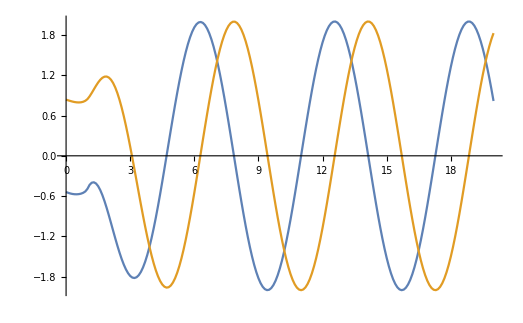

```mathematica
xs = Range[0.0,20.0,0.1];
result = integrateA[0,#]&/@xs;
ListPlot[ {{xs,Re[result]}ᵀ,{xs,Im[result]}ᵀ},Joined->True]
```